```mathematica
MRtab=Import[StringJoin[NotebookDirectory[],"Mann2015_Tables5_6_7.txt"],"Data"][[68;;All]];
MRtab=Table[ToExpression[StringSplit[StringJoin[Characters[First[MRtab[[i]]]][[74;;101]]]," "]],{i,1,Length[MRtab]}];
MRtab=Select[MRtab,#[[1]]>0&&#[[3]]>0&];
MRtab=Table[{MRtab[[i,3]],MRtab[[i,4]],MRtab[[i,1]],MRtab[[i,2]]},{i,1,Length[MRtab]}];
```

```mathematica
MRtab=Select[MRtab,#[[1]]>0.12&];
```

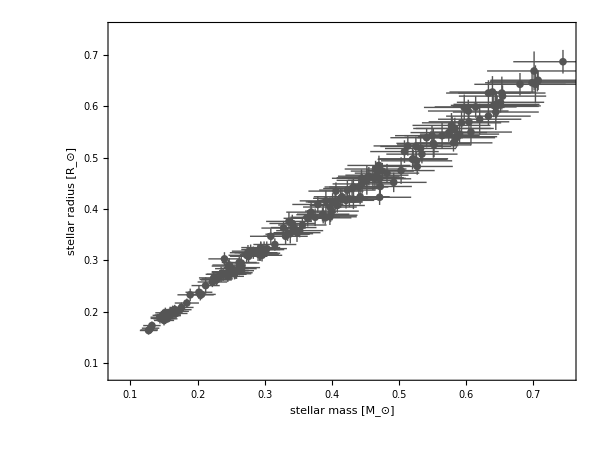

```mathematica
MRtab2=Table[{Around[MRtab[[i,1]],MRtab[[i,2]]],Around[MRtab[[i,3]],MRtab[[i,4]]]},{i,1,Length[MRtab]}];
xticks=Table[{x,ToString[x]},{x,0.1,0.7,0.1}];
xticks2=Table[{x,""},{x,0.1,0.7,0.1}];
ListPlot[MRtab2,PlotRange->{{0.08,0.75},{0.08,0.75}},ImageSize->{600,Automatic},AspectRatio->0.75,Frame->True,FrameLabel->{"stellar mass [M_⊙]","stellar radius [R_⊙]"},FrameTicks->{{xticks,xticks2},{xticks,xticks2}},FrameStyle->Lighter[Black],BaseStyle->{FontFamily->"CMU Serif",Lighter[Black],FontSize->24},PlotStyle->Lighter[Black]]
```

```mathematica
mannchain=Import[StringJoin[NotebookDirectory[],"mr_correlated.dat"],"Table"];
mannchain2=Table[{mannchain[[i,1]] Sec[mannchain[[i,2]]],Tan[mannchain[[i,2]]],√Exp[mannchain[[i,3]]],mannchain[[i,4]]},{i,1,Length[mannchain]}];
Max[mannchain2[[All,4]]]
bestrow=Last[Sort[mannchain2,#1[[4]]<#2[[4]]&]]
```

710.178

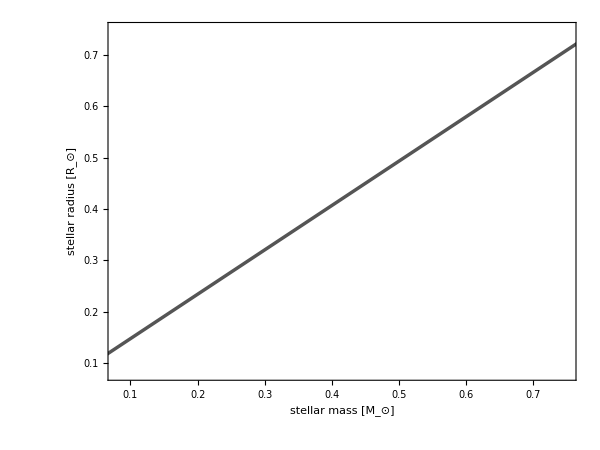

```mathematica
Plot[{bestrow[[1]]+bestrow[[2]]*M-0.5bestrow[[3]],bestrow[[1]]+bestrow[[2]]*M+0.5bestrow[[3]]},{M,0,1},PlotRange->{{0.08,0.75},{0.08,0.75}},ImageSize->{600,Automatic},AspectRatio->0.75,Frame->True,FrameLabel->{"stellar mass [M_⊙]","stellar radius [R_⊙]"},FrameTicks->{{xticks,xticks2},{xticks,xticks2}},FrameStyle->Black,BaseStyle->{FontFamily->"CMU Serif",Lighter[Black],FontSize->24},PlotStyle->Lighter[Black]]
```

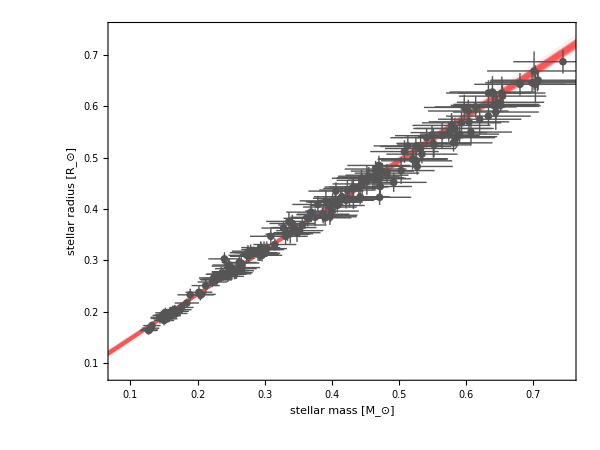

```mathematica
samples=RandomSample[mannchain2,100];
export=Show[Table[Plot[samples[[i,1]]+samples[[i,2]]*M,{M,0,1},PlotRange->{{0.08,0.75},{0.08,0.75}},ImageSize->{600,Automatic},AspectRatio->0.75,Frame->True,FrameLabel->{"stellar mass [M_⊙]","stellar radius [R_⊙]"},FrameTicks->{{xticks,xticks2},{xticks,xticks2}},FrameStyle->Black,BaseStyle->{FontFamily->"CMU Serif",Lighter[Black],FontSize->24},PlotStyle->Directive[Lighter[Red],Opacity[0.1]]],{i,1,100}],ListPlot[MRtab2,PlotRange->{{0.08,0.75},{0.08,0.75}},ImageSize->{600,Automatic},AspectRatio->0.75,Frame->True,FrameLabel->{"stellar mass [M_⊙]","stellar radius [R_⊙]"},FrameTicks->{{xticks,xticks2},{xticks,xticks2}},FrameStyle->Lighter[Black],BaseStyle->{FontFamily->"CMU Serif",Lighter[Black],FontSize->24},PlotStyle->Lighter[Black]]]
```

```mathematica
Export[StringJoin[NotebookDirectory[],"mann_fit.pdf"],export]
```